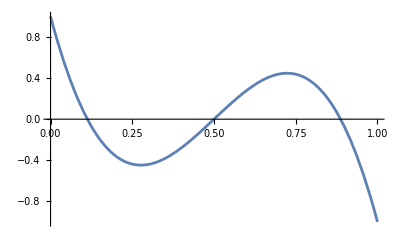

```mathematica
ϕ0[ζ_]=(-1)^0 LegendreP[0,2*ζ-1];
ϕ1[ζ_]=(-1)^1 LegendreP[1,2*ζ-1];
ϕ2[ζ_]=(-1)^2 LegendreP[2,2*ζ-1];
ϕ3[ζ_]=(-1)^3 LegendreP[3,2*ζ-1];
Plot[ϕ3[ζ],{ζ,0,1}]
```

```mathematica
Integrate[ϕ3[ζ]*ϕ1[ζ],{ζ,0,a}]
```

a-7 a^2+18 a^3-20 a^4+8 a^5

```mathematica
integrandValues1 = Table[Integrate[(-1)^i LegendreP[i,2*ζ-1]*(-1)^j LegendreP[j,2*ζ-1],{ζ,0,a}],{i,1,7},{j,1,7}];
integrandValues2 = Table[Integrate[(-1)^i LegendreP[i,2*ζ-1],{ζ,0,a}],{i,1,7}];
```

```mathematica
integrandValues1/.{a->h_r}//MatrixForm
```

(h_r-2 h_r^2+(4 h_r^3)/3 | h_r-4 h_r^2+6 h_r^3-3 h_r^4 | h_r-7 h_r^2+18 h_r^3-20 h_r^4+8 h_r^5 | h_r-11 h_r^2+(130 h_r^3)/3-80 h_r^4+70 h_r^5-(70 h_r^6)/3 | h_r-16 h_r^2+90 h_r^3-245 h_r^4+350 h_r^5-252 h_r^6+72 h_r^7 | h_r-22 h_r^2+168 h_r^3-630 h_r^4+1302 h_r^5-1512 h_r^6+924 h_r^7-231 h_r^8 | h_r-29 h_r^2+(868 h_r^3)/3-1428 h_r^4+3990 h_r^5-6622 h_r^6+6468 h_r^7-3432 h_r^8+(2288 h_r^9)/3
h_r-4 h_r^2+6 h_r^3-3 h_r^4 | h_r-6 h_r^2+16 h_r^3-18 h_r^4+(36 h_r^5)/5 | h_r-9 h_r^2+36 h_r^3-68 h_r^4+60 h_r^5-20 h_r^6 | h_r-13 h_r^2+72 h_r^3-200 h_r^4+290 h_r^5-210 h_r^6+60 h_r^7 | h_r-18 h_r^2+132 h_r^3-500 h_r^4+1050 h_r^5-1232 h_r^6+756 h_r^7-189 h_r^8 | h_r-24 h_r^2+226 h_r^3-1113 h_r^4+3150 h_r^5-5292 h_r^6+5208 h_r^7-2772 h_r^8+616 h_r^9 | h_r-31 h_r^2+366 h_r^3-2268 h_r^4+(41286 h_r^5)/5-18522 h_r^6+25872 h_r^7-21912 h_r^8+10296 h_r^9-(10296 h_r^10)/5
h_r-7 h_r^2+18 h_r^3-20 h_r^4+8 h_r^5 | h_r-9 h_r^2+36 h_r^3-68 h_r^4+60 h_r^5-20 h_r^6 | h_r-12 h_r^2+68 h_r^3-190 h_r^4+276 h_r^5-200 h_r^6+(400 h_r^7)/7 | h_r-16 h_r^2+120 h_r^3-460 h_r^4+970 h_r^5-1140 h_r^6+700 h_r^7-175 h_r^8 | h_r-21 h_r^2+200 h_r^3-1000 h_r^4+2850 h_r^5-4802 h_r^6+4732 h_r^7-2520 h_r^8+560 h_r^9 | h_r-27 h_r^2+318 h_r^3-2000 h_r^4+7350 h_r^5-16562 h_r^6+23184 h_r^7-19656 h_r^8+9240 h_r^9-1848 h_r^10 | h_r-34 h_r^2+486 h_r^3-3743 h_r^4+17150 h_r^5-49392 h_r^6+91728 h_r^7-109692 h_r^8+81576 h_r^9-34320 h_r^10+6240 h_r^11
h_r-11 h_r^2+(130 h_r^3)/3-80 h_r^4+70 h_r^5-(70 h_r^6)/3 | h_r-13 h_r^2+72 h_r^3-200 h_r^4+290 h_r^5-210 h_r^6+60 h_r^7 | h_r-16 h_r^2+120 h_r^3-460 h_r^4+970 h_r^5-1140 h_r^6+700 h_r^7-175 h_r^8 | h_r-20 h_r^2+(580 h_r^3)/3-970 h_r^4+2768 h_r^5-(14000 h_r^6)/3+4600 h_r^7-2450 h_r^8+(4900 h_r^9)/9 | h_r-25 h_r^2+300 h_r^3-1900 h_r^4+7000 h_r^5-15792 h_r^6+22120 h_r^7-18760 h_r^8+8820 h_r^9-1764 h_r^10 | h_r-31 h_r^2+450 h_r^3-3500 h_r^4+16100 h_r^5-46452 h_r^6+86352 h_r^7-103320 h_r^8+76860 h_r^9-32340 h_r^10+5880 h_r^11 | h_r-38 h_r^2+(1966 h_r^3)/3-6125 h_r^4+34300 h_r^5-(367696 h_r^6)/3+289296 h_r^7-456444 h_r^8+476300 h_r^9-315480 h_r^10+120120 h_r^11-20020 h_r^12
h_r-16 h_r^2+90 h_r^3-245 h_r^4+350 h_r^5-252 h_r^6+72 h_r^7 | h_r-18 h_r^2+132 h_r^3-500 h_r^4+1050 h_r^5-1232 h_r^6+756 h_r^7-189 h_r^8 | h_r-21 h_r^2+200 h_r^3-1000 h_r^4+2850 h_r^5-4802 h_r^6+4732 h_r^7-2520 h_r^8+560 h_r^9 | h_r-25 h_r^2+300 h_r^3-1900 h_r^4+7000 h_r^5-15792 h_r^6+22120 h_r^7-18760 h_r^8+8820 h_r^9-1764 h_r^10 | h_r-30 h_r^2+440 h_r^3-3430 h_r^4+15792 h_r^5-45584 h_r^6+84760 h_r^7-101430 h_r^8+75460 h_r^9-31752 h_r^10+(63504 h_r^11)/11 | h_r-36 h_r^2+630 h_r^3-5915 h_r^4+33180 h_r^5-118664 h_r^6+280224 h_r^7-442260 h_r^8+461580 h_r^9-305760 h_r^10+116424 h_r^11-19404 h_r^12 | h_r-43 h_r^2+882 h_r^3-9800 h_r^4+65660 h_r^5-284004 h_r^6+825552 h_r^7-1645128 h_r^8+2252700 h_r^9-2083620 h_r^10+1243704 h_r^11-432432 h_r^12+66528 h_r^13
h_r-22 h_r^2+168 h_r^3-630 h_r^4+1302 h_r^5-1512 h_r^6+924 h_r^7-231 h_r^8 | h_r-24 h_r^2+226 h_r^3-1113 h_r^4+3150 h_r^5-5292 h_r^6+5208 h_r^7-2772 h_r^8+616 h_r^9 | h_r-27 h_r^2+318 h_r^3-2000 h_r^4+7350 h_r^5-16562 h_r^6+23184 h_r^7-19656 h_r^8+9240 h_r^9-1848 h_r^10 | h_r-31 h_r^2+450 h_r^3-3500 h_r^4+16100 h_r^5-46452 h_r^6+86352 h_r^7-103320 h_r^8+76860 h_r^9-32340 h_r^10+5880 h_r^11 | h_r-36 h_r^2+630 h_r^3-5915 h_r^4+33180 h_r^5-118664 h_r^6+280224 h_r^7-442260 h_r^8+461580 h_r^9-305760 h_r^10+116424 h_r^11-19404 h_r^12 | h_r-42 h_r^2+868 h_r^3-9660 h_r^4+64764 h_r^5-280224 h_r^6+814728 h_r^7-1623762 h_r^8+2223620 h_r^9-2056824 h_r^10+1227744 h_r^11-426888 h_r^12+(853776 h_r^13)/13 | h_r-49 h_r^2+1176 h_r^3-15288 h_r^4+120540 h_r^5-619164 h_r^6+2165016 h_r^7-5284344 h_r^8+9094932 h_r^9-10990980 h_r^10+9125424 h_r^11-4956336 h_r^12+1585584 h_r^13-226512 h_r^14
h_r-29 h_r^2+(868 h_r^3)/3-1428 h_r^4+3990 h_r^5-6622 h_r^6+6468 h_r^7-3432 h_r^8+(2288 h_r^9)/3 | h_r-31 h_r^2+366 h_r^3-2268 h_r^4+(41286 h_r^5)/5-18522 h_r^6+25872 h_r^7-21912 h_r^8+10296 h_r^9-(10296 h_r^10)/5 | h_r-34 h_r^2+486 h_r^3-3743 h_r^4+17150 h_r^5-49392 h_r^6+91728 h_r^7-109692 h_r^8+81576 h_r^9-34320 h_r^10+6240 h_r^11 | h_r-38 h_r^2+(1966 h_r^3)/3-6125 h_r^4+34300 h_r^5-(367696 h_r^6)/3+289296 h_r^7-456444 h_r^8+476300 h_r^9-315480 h_r^10+120120 h_r^11-20020 h_r^12 | h_r-43 h_r^2+882 h_r^3-9800 h_r^4+65660 h_r^5-284004 h_r^6+825552 h_r^7-1645128 h_r^8+2252700 h_r^9-2083620 h_r^10+1243704 h_r^11-432432 h_r^12+66528 h_r^13 | h_r-49 h_r^2+1176 h_r^3-15288 h_r^4+120540 h_r^5-619164 h_r^6+2165016 h_r^7-5284344 h_r^8+9094932 h_r^9-10990980 h_r^10+9125424 h_r^11-4956336 h_r^12+1585584 h_r^13-226512 h_r^14 | h_r-56 h_r^2+(4648 h_r^3)/3-23268 h_r^4+(1065036 h_r^5)/5-1279544 h_r^6+5284344 h_r^7-15439974 h_r^8+(97219276 h_r^9)/3-(245144592 h_r^10)/5+52993584 h_r^11-39903864 h_r^12+19880784 h_r^13-5889312 h_r^14+(3926208 h_r^15)/5)

```mathematica
i=0;
j=1;
integrandValues1[[i+1,j+1]]
```

a-4 a^2+6 a^3-3 a^4

```mathematica
order= 7;
NumberOfEntries=order*(order+1)/2;
OutputPythonElements=ConstantArray[0,{NumberOfEntries,1}];
k=1;
For[i=1,i<=order,i++,
For[j=1,j<i,j++,
OutputPythonElements[[k++,1]]=integrandValues1[[i,j]];];
OutputPythonElements[[k++,1]]=integrandValues1[[i,i]];
]
OutputPython = StringReplace[ToString[CForm[OutputPythonElements]],{"a"->"h_r","Power(a,2)"->"h_r**2","Power(a,3)"->"h_r**3","Power(a,4)"->"h_r**4","Power(a,5)"->"h_r**5","Power(a,6)"->"h_r**6","Power(a,7)"->"h_r**7","Power(a,8)"->"h_r**8","Power(a,9)"->"h_r**9","Power(a,10)"->"h_r**10","Power(a,11)"->"h_r**11","Power(a,12)"->"h_r**12","Power(a,13)"->"h_r**13","Power(a,14)"->"h_r**14","Power(a,15)"->"h_r**15","List(List("->"integrals[] = integrals[] = ","),List("->"\nintegrals[] = integrals[] = "}];
For[i=0,i <order,i++,
For[j=0,j<i,j++,
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],"][",ToString[j]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[j],"][",ToString[i]],StringPosition[OutputPython,"integrals[]",1][[1,2]]]];
OutputPython=StringReplace[OutputPython,{"integrals[] = "->""},1];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],"][",ToString[i]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
];

OutputPython
```

integrals[0][0] = h_r - 2*h_r**2 + (4*h_r**3)/3.
integrals[1][0] = integrals[0][1] = h_r - 4*h_r**2 + 6*h_r**3 - 3*h_r**4
integrals[1][1] = h_r - 6*h_r**2 + 16*h_r**3 - 18*h_r**4 + (36*h_r**5)/5.
integrals[2][0] = integrals[0][2] = h_r - 7*h_r**2 + 18*h_r**3 - 20*h_r**4 + 8*h_r**5
integrals[2][1] = integrals[1][2] = h_r - 9*h_r**2 + 36*h_r**3 - 68*h_r**4 + 60*h_r**5 - 20*h_r**6
integrals[2][2] = h_r - 12*h_r**2 + 68*h_r**3 - 190*h_r**4 + 276*h_r**5 - 200*h_r**6 + (400*h_r**7)/7.
integrals[3][0] = integrals[0][3] = h_r - 11*h_r**2 + (130*h_r**3)/3. - 80*h_r**4 + 70*h_r**5 - (70*h_r**6)/3.
integrals[3][1] = integrals[1][3] = h_r - 13*h_r**2 + 72*h_r**3 - 200*h_r**4 + 290*h_r**5 - 210*h_r**6 + 60*h_r**7
integrals[3][2] = integrals[2][3] = h_r - 16*h_r**2 + 120*h_r**3 - 460*h_r**4 + 970*h_r**5 - 1140*h_r**6 + 700*h_r**7 - 175*h_r**8
integrals[3][3] = h_r - 20*h_r**2 + (580*h_r**3)/3. - 970*h_r**4 + 2768*h_r**5 - (14000*h_r**6)/3. + 4600*h_r**7 - 2450*h_r**8 + (4900*h_r**9)/9.
integrals[4][0] = integrals[0][4] = h_r - 16*h_r**2 + 90*h_r**3 - 245*h_r**4 + 350*h_r**5 - 252*h_r**6 + 72*h_r**7
integrals[4][1] = integrals[1][4] = h_r - 18*h_r**2 + 132*h_r**3 - 500*h_r**4 + 1050*h_r**5 - 1232*h_r**6 + 756*h_r**7 - 189*h_r**8
integrals[4][2] = integrals[2][4] = h_r - 21*h_r**2 + 200*h_r**3 - 1000*h_r**4 + 2850*h_r**5 - 4802*h_r**6 + 4732*h_r**7 - 2520*h_r**8 + 560*h_r**9
integrals[4][3] = integrals[3][4] = h_r - 25*h_r**2 + 300*h_r**3 - 1900*h_r**4 + 7000*h_r**5 - 15792*h_r**6 + 22120*h_r**7 - 18760*h_r**8 + 8820*h_r**9 - 1764*h_r**10
integrals[4][4] = h_r - 30*h_r**2 + 440*h_r**3 - 3430*h_r**4 + 15792*h_r**5 - 45584*h_r**6 + 84760*h_r**7 - 101430*h_r**8 + 75460*h_r**9 - 31752*h_r**10 + (63504*h_r**11)/11.
integrals[5][0] = integrals[0][5] = h_r - 22*h_r**2 + 168*h_r**3 - 630*h_r**4 + 1302*h_r**5 - 1512*h_r**6 + 924*h_r**7 - 231*h_r**8
integrals[5][1] = integrals[1][5] = h_r - 24*h_r**2 + 226*h_r**3 - 1113*h_r**4 + 3150*h_r**5 - 5292*h_r**6 + 5208*h_r**7 - 2772*h_r**8 + 616*h_r**9
integrals[5][2] = integrals[2][5] = h_r - 27*h_r**2 + 318*h_r**3 - 2000*h_r**4 + 7350*h_r**5 - 16562*h_r**6 + 23184*h_r**7 - 19656*h_r**8 + 9240*h_r**9 - 1848*h_r**10
integrals[5][3] = integrals[3][5] = h_r - 31*h_r**2 + 450*h_r**3 - 3500*h_r**4 + 16100*h_r**5 - 46452*h_r**6 + 86352*h_r**7 - 103320*h_r**8 + 76860*h_r**9 - 32340*h_r**10 + 5880*h_r**11
integrals[5][4] = integrals[4][5] = h_r - 36*h_r**2 + 630*h_r**3 - 5915*h_r**4 + 33180*h_r**5 - 118664*h_r**6 + 280224*h_r**7 - 442260*h_r**8 + 461580*h_r**9 - 305760*h_r**10 + 116424*h_r**11 - 19404*h_r**12
integrals[5][5] = h_r - 42*h_r**2 + 868*h_r**3 - 9660*h_r**4 + 64764*h_r**5 - 280224*h_r**6 + 814728*h_r**7 - 1623762*h_r**8 + 2223620*h_r**9 - 2056824*h_r**10 + 1227744*h_r**11 - 426888*h_r**12 + (853776*h_r**13)/13.
integrals[6][0] = integrals[0][6] = h_r - 29*h_r**2 + (868*h_r**3)/3. - 1428*h_r**4 + 3990*h_r**5 - 6622*h_r**6 + 6468*h_r**7 - 3432*h_r**8 + (2288*h_r**9)/3.
integrals[6][1] = integrals[1][6] = h_r - 31*h_r**2 + 366*h_r**3 - 2268*h_r**4 + (41286*h_r**5)/5. - 18522*h_r**6 + 25872*h_r**7 - 21912*h_r**8 + 10296*h_r**9 - (10296*h_r**10)/5.
integrals[6][2] = integrals[2][6] = h_r - 34*h_r**2 + 486*h_r**3 - 3743*h_r**4 + 17150*h_r**5 - 49392*h_r**6 + 91728*h_r**7 - 109692*h_r**8 + 81576*h_r**9 - 34320*h_r**10 + 6240*h_r**11
integrals[6][3] = integrals[3][6] = h_r - 38*h_r**2 + (1966*h_r**3)/3. - 6125*h_r**4 + 34300*h_r**5 - (367696*h_r**6)/3. + 289296*h_r**7 - 456444*h_r**8 + 476300*h_r**9 - 315480*h_r**10 + 120120*h_r**11 - 20020*h_r**12
integrals[6][4] = integrals[4][6] = h_r - 43*h_r**2 + 882*h_r**3 - 9800*h_r**4 + 65660*h_r**5 - 284004*h_r**6 + 825552*h_r**7 - 1645128*h_r**8 + 2252700*h_r**9 - 2083620*h_r**10 + 1243704*h_r**11 - 432432*h_r**12 + 66528*h_r**13
integrals[6][5] = integrals[5][6] = h_r - 49*h_r**2 + 1176*h_r**3 - 15288*h_r**4 + 120540*h_r**5 - 619164*h_r**6 + 2165016*h_r**7 - 5284344*h_r**8 + 9094932*h_r**9 - 10990980*h_r**10 + 9125424*h_r**11 - 4956336*h_r**12 + 1585584*h_r**13 - 226512*h_r**14
integrals[6][6] = h_r - 56*h_r**2 + (4648*h_r**3)/3. - 23268*h_r**4 + (1065036*h_r**5)/5. - 1279544*h_r**6 + 5284344*h_r**7 - 15439974*h_r**8 + (97219276*h_r**9)/3. - (245144592*h_r**10)/5. + 52993584*h_r**11 - 39903864*h_r**12 + 19880784*h_r**13 - 5889312*h_r**14 + (3926208*h_r**15)/5.))

```mathematica
0.7^10
```

0.0282475